```mathematica
psi[m_,x_]=HermiteH[m,x]/(√(2^m*m!√π))Exp[-x^2/2]; (*wave functions in the Fock basis*)
```

```mathematica
Tpsi=Table[psi[m,x],{m,0,16}];
```

```mathematica
n=10;
```

```mathematica
rho=Table[ KroneckerDelta[a,b]/(n+1),{a,0,n},{b,0,n}] 
(* starting density matrix in the Fock basis *)
```

{{1/11,0,0,0,0,0,0,0,0,0,0},{0,1/11,0,0,0,0,0,0,0,0,0},{0,0,1/11,0,0,0,0,0,0,0,0},{0,0,0,1/11,0,0,0,0,0,0,0},{0,0,0,0,1/11,0,0,0,0,0,0},{0,0,0,0,0,1/11,0,0,0,0,0},{0,0,0,0,0,0,1/11,0,0,0,0},{0,0,0,0,0,0,0,1/11,0,0,0},{0,0,0,0,0,0,0,0,1/11,0,0},{0,0,0,0,0,0,0,0,0,1/11,0},{0,0,0,0,0,0,0,0,0,0,1/11}}

```mathematica
Proj=Table[(Tpsi[[a+1]]Tpsi[[b+1]])ⅇ^(ⅈ(b-a)theta),{a,0,n},{b,0,n}] ;
```

```mathematica
prob=∑_(b=0)^n ∑_(a=0)^n rho[[b+1,a+1]]Proj[[a+1,b+1]]
```

(ⅇ^(-x^2))/(11 √π)+(2 ⅇ^(-x^2) x^2)/(11 √π)+(ⅇ^(-x^2) (-2+4 x^2)^2)/(88 √π)+(ⅇ^(-x^2) (-12 x+8 x^3)^2)/(528 √π)+(ⅇ^(-x^2) (12-48 x^2+16 x^4)^2)/(4224 √π)+(ⅇ^(-x^2) (120 x-160 x^3+32 x^5)^2)/(42240 √π)+(ⅇ^(-x^2) (-120+720 x^2-480 x^4+64 x^6)^2)/(506880 √π)+(ⅇ^(-x^2) (-1680 x+3360 x^3-1344 x^5+128 x^7)^2)/(7096320 √π)+(ⅇ^(-x^2) (1680-13440 x^2+13440 x^4-3584 x^6+256 x^8)^2)/(113541120 √π)+(ⅇ^(-x^2) (30240 x-80640 x^3+48384 x^5-9216 x^7+512 x^9)^2)/(2043740160 √π)+(ⅇ^(-x^2) (-30240+302400 x^2-403200 x^4+161280 x^6-23040 x^8+1024 x^10)^2)/(40874803200 √π)

```mathematica
Data=Extract[Import["C:/sqzfinal10000.txt","Table"],1];
dataSh=Extract[Import["C:/shotfinal10000.txt","Table"],1];
```

```mathematica
Media=Mean[dataSh]
SQL=StandardDeviation[dataSh]
```

-0.0000434907

0.00322232

```mathematica
(*NB:data must be normalized in order to have the shot noise(=variance of the vacuum) equal to 1/2*)
```

```mathematica
(*check the shot noise variance*)
Variance[(dataSh-Media)/SQL*1/(√2)]
```

0.5

```mathematica
data=(Data-Media)/SQL*1/(√2);
```

```mathematica
ldata=Length[data];
```

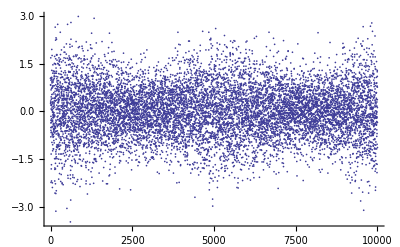

```mathematica
ListPlot[data,PlotStyle->{PointSize[0.003]}]
```

```mathematica
(*create the marginal distibutions*)
```

```mathematica
Nbin=100;
```

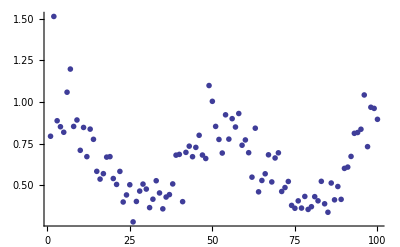

```mathematica
Do[Marginal[j]=Partition[data,10000/Nbin][[j]],{j,1,Nbin}];
Rumore=Table[Variance[Marginal[j]],{j,1,Nbin}];
ListPlot[Rumore,PlotStyle->{PointSize[0.01]}]
```

```mathematica
(*compute the sqeezing with respect to the shot noise level*)
```

```mathematica
10*Log[10,Min[Rumore]/(1/2)]
```

-2.52933

```mathematica
Minsx=Extract[Extract[Position[Partition[Rumore,Nbin/2][[1]],Min[Partition[Rumore,Nbin/2][[1]]]],1],1]
Mindx=Extract[Extract[Nbin/2+Position[Partition[Rumore,Nbin/2][[2]],Min[Partition[Rumore,Nbin/2][[2]]]],1],1]
```

26

85

```mathematica
(*phase estimation in unity of 2Pi*)
DeltaPhi=(Pi*Nbin)/(Abs[Mindx-Minsx]*2*π)//N
```

0.847458

```mathematica
Angoli=Table[(j-1)*(DeltaPhi*2*π)/(ldata-1),{j,1,ldata}];
```

```mathematica
Angoli[[2400]]
```

1.27753

```mathematica
Zoom=Table[data[[w]],{w,2000,3000}];
```

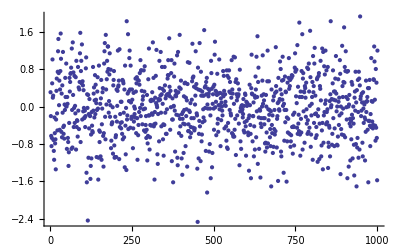

```mathematica
ListPlot[Zoom]
```

```mathematica
Pi/2//N
```

1.5708

```mathematica
(*initial likelyhood logarithm*)
lnL=∑_(k=1)^ldata Log[prob/.{x->data[[k]],theta->Angoli[[k]] }]
```

-20127.3

```mathematica
(*NB: As a preliminar test, I checked the rho function for the coherent vacuum: the reconstructed function is consistent with rho=Diag(1,0,0,0) *)
```

```mathematica
For[i=1,i<11,i++,Print[MatrixForm[rho]];
prob=∑_(b=0)^n ∑_(a=0)^n rho[[b+1,a+1]]Proj[[a+1,b+1]];
lnL=∑_(k=1)^ldata Log[prob/.{x->data[[k]],theta->Angoli[[k]] }];Print[lnL];R=Table[∑_(k=1)^ldata 1/(prob/.{x->data[[k]],theta->Angoli[[k]] })(Proj[[a+1,b+1]] /.{x->data[[k]],theta->Angoli[[k]] }),{a,0,n},{b,0,n}];rho=R.rho.R/Tr[R.rho.R] ];
```

(1/11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/11 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/11 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/11 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/11 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/11 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/11 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/11 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/11)

-20127.3

(0.499683-4.07755×10^-19 ⅈ | 0.00229737+0.00364944 ⅈ | 0.0463808-0.0446229 ⅈ | -0.00328099-0.000891715 ⅈ | 0.00359641-0.00629771 ⅈ | -0.00151187+0.000408161 ⅈ | -0.00122554-0.00167435 ⅈ | 0.00177012-0.00177926 ⅈ | 0.0024461+0.000186381 ⅈ | -0.000296199+0.0000473461 ⅈ | -0.00141784-0.00240087 ⅈ
0.00229737-0.00364944 ⅈ | 0.149328-1.0149×10^-19 ⅈ | 0.00083262-0.000746783 ⅈ | 0.0179176-0.0192478 ⅈ | -0.00107589-0.000917766 ⅈ | 0.00157298+0.00173392 ⅈ | 0.00088848+0.000966588 ⅈ | -0.000913594+0.000202478 ⅈ | 0.000821948+0.000609126 ⅈ | 0.000036805+0.00150378 ⅈ | -0.00104971+0.00036955 ⅈ
0.0463808+0.0446229 ⅈ | 0.00083262+0.000746783 ⅈ | 0.0905093+4.03502×10^-19 ⅈ | 0.000655364+0.00072596 ⅈ | 0.0123394-0.0139025 ⅈ | -0.000352464-0.00130039 ⅈ | 0.000800926+0.000453336 ⅈ | 0.0000194909-0.000808269 ⅈ | 0.00122092+0.00103589 ⅈ | -0.000723604+0.00097047 ⅈ | 0.000274852-0.000166321 ⅈ
-0.00328099+0.000891715 ⅈ | 0.0179176+0.0192478 ⅈ | 0.000655364-0.00072596 ⅈ | 0.0604324+1.04599×10^-19 ⅈ | -0.000547655-0.000804082 ⅈ | 0.00754705-0.00944378 ⅈ | -0.000467314-0.000284455 ⅈ | 0.00160155+0.00139728 ⅈ | 0.00027116+0.000381601 ⅈ | -0.000853576-0.000702744 ⅈ | 0.000679949-0.000732557 ⅈ
0.00359641+0.00629771 ⅈ | -0.00107589+0.000917766 ⅈ | 0.0123394+0.0139025 ⅈ | -0.000547655+0.000804082 ⅈ | 0.0460527+1.28331×10^-21 ⅈ | -0.000156733+0.000477242 ⅈ | 0.00647575-0.00829313 ⅈ | 0.0000976119-0.000428249 ⅈ | 0.000302291+0.00189652 ⅈ | 0.000120551-0.0000581064 ⅈ | 0.000402127+0.000490398 ⅈ
-0.00151187-0.000408161 ⅈ | 0.00157298-0.00173392 ⅈ | -0.000352464+0.00130039 ⅈ | 0.00754705+0.00944378 ⅈ | -0.000156733-0.000477242 ⅈ | 0.0360457-2.11557×10^-22 ⅈ | 0.000386576-0.000232616 ⅈ | 0.00503236-0.00643002 ⅈ | -0.000386078-0.000219582 ⅈ | 0.00149666+0.00113561 ⅈ | 0.0000955426-0.000318768 ⅈ
-0.00122554+0.00167435 ⅈ | 0.00088848-0.000966588 ⅈ | 0.000800926-0.000453336 ⅈ | -0.000467314+0.000284455 ⅈ | 0.00647575+0.00829313 ⅈ | 0.000386576+0.000232616 ⅈ | 0.0307842-1.75893×10^-21 ⅈ | 0.0000609403+0.00011424 ⅈ | 0.00428258-0.00572477 ⅈ | 0.0000441656-0.000390319 ⅈ | 0.000357789+0.00185305 ⅈ
0.00177012+0.00177926 ⅈ | -0.000913594-0.000202478 ⅈ | 0.0000194909+0.000808269 ⅈ | 0.00160155-0.00139728 ⅈ | 0.0000976119+0.000428249 ⅈ | 0.00503236+0.00643002 ⅈ | 0.0000609403-0.00011424 ⅈ | 0.026316-1.42122×10^-22 ⅈ | -0.000365746-0.0000569434 ⅈ | 0.00393447-0.00507284 ⅈ | -0.000159092-0.0000562294 ⅈ
0.0024461-0.000186381 ⅈ | 0.000821948-0.000609126 ⅈ | 0.00122092-0.00103589 ⅈ | 0.00027116-0.000381601 ⅈ | 0.000302291-0.00189652 ⅈ | -0.000386078+0.000219582 ⅈ | 0.00428258+0.00572477 ⅈ | -0.000365746+0.0000569434 ⅈ | 0.0227262-1.33383×10^-22 ⅈ | 0.000423873+0.0000929752 ⅈ | 0.00316773-0.00459216 ⅈ
-0.000296199-0.0000473461 ⅈ | 0.000036805-0.00150378 ⅈ | -0.000723604-0.00097047 ⅈ | -0.000853576+0.000702744 ⅈ | 0.000120551+0.0000581064 ⅈ | 0.00149666-0.00113561 ⅈ | 0.0000441656+0.000390319 ⅈ | 0.00393447+0.00507284 ⅈ | 0.000423873-0.0000929752 ⅈ | 0.0207096-1.70868×10^-22 ⅈ | -0.000342484-0.0000702167 ⅈ
-0.00141784+0.00240087 ⅈ | -0.00104971-0.00036955 ⅈ | 0.000274852+0.000166321 ⅈ | 0.000679949+0.000732557 ⅈ | 0.000402127-0.000490398 ⅈ | 0.0000955426+0.000318768 ⅈ | 0.000357789-0.00185305 ⅈ | -0.000159092+0.0000562294 ⅈ | 0.00316773+0.00459216 ⅈ | -0.000342484+0.0000702167 ⅈ | 0.0174122+2.27752×10^-21 ⅈ)

-13789.3-2.68434×10^-15 ⅈ

(0.77392-4.59344×10^-19 ⅈ | 0.00432897+0.00600886 ⅈ | 0.0697296-0.06146 ⅈ | -0.00551913-0.000481461 ⅈ | 0.00395619-0.0135009 ⅈ | -0.00279564+0.00105349 ⅈ | -0.00284864-0.0030838 ⅈ | 0.00298952-0.00323178 ⅈ | 0.00420698+0.000751004 ⅈ | -0.0013182+0.00132538 ⅈ | -0.00194129-0.00263654 ⅈ
0.00432897-0.00600886 ⅈ | 0.121536-2.36996×10^-19 ⅈ | 0.00130355-0.00115467 ⅈ | 0.0163551-0.015745 ⅈ | -0.00118927-0.0010833 ⅈ | 0.000583836-0.000333729 ⅈ | 0.000590437+0.000760233 ⅈ | -0.000498086+0.000473047 ⅈ | 0.000405765+0.000977368 ⅈ | 0.0000844664+0.00115692 ⅈ | -0.000906992+0.000360035 ⅈ
0.0697296+0.06146 ⅈ | 0.00130355+0.00115467 ⅈ | 0.0493543+6.99049×10^-19 ⅈ | 0.000204427+0.000107189 ⅈ | 0.00766931-0.0079237 ⅈ | -0.000295185-0.0010474 ⅈ | 0.00013914-0.00113201 ⅈ | 0.000351171-0.000620421 ⅈ | 0.00093247+0.000964656 ⅈ | -0.00082505+0.000617203 ⅈ | 0.000137316-0.000317189 ⅈ
-0.00551913+0.000481461 ⅈ | 0.0163551+0.015745 ⅈ | 0.000204427-0.000107189 ⅈ | 0.0213596-1.01264×10^-20 ⅈ | -0.000632579-0.000590214 ⅈ | 0.00275808-0.00352575 ⅈ | -0.000111884-0.0000885946 ⅈ | 0.00033741+0.0000515809 ⅈ | 0.0000423749+0.000250135 ⅈ | -0.000390397-0.000276827 ⅈ | 0.000132697-0.0003614 ⅈ
0.00395619+0.0135009 ⅈ | -0.00118927+0.0010833 ⅈ | 0.00766931+0.0079237 ⅈ | -0.000632579+0.000590214 ⅈ | 0.0119676+8.36946×10^-21 ⅈ | -0.000112795+0.000099019 ⅈ | 0.00186683-0.00258115 ⅈ | 0.000147397-0.000100052 ⅈ | -0.0000123958+0.000450407 ⅈ | -0.0000754105-0.0000780284 ⅈ | 0.000231277+0.0000486098 ⅈ
-0.00279564-0.00105349 ⅈ | 0.000583836+0.000333729 ⅈ | -0.000295185+0.0010474 ⅈ | 0.00275808+0.00352575 ⅈ | -0.000112795-0.000099019 ⅈ | 0.00684551+2.04175×10^-20 ⅈ | 0.00021009-0.0000382987 ⅈ | 0.00109157-0.00146623 ⅈ | -0.000115477-0.0000599094 ⅈ | 0.000311435+9.41083×10^-6 ⅈ | 0.0000873451-0.000121015 ⅈ
-0.00284864+0.0030838 ⅈ | 0.000590437-0.000760233 ⅈ | 0.00013914+0.00113201 ⅈ | -0.000111884+0.0000885946 ⅈ | 0.00186683+0.00258115 ⅈ | 0.00021009+0.0000382987 ⅈ | 0.00500189+1.31808×10^-20 ⅈ | -1.15677×10^-6+0.0000348155 ⅈ | 0.000737076-0.00110347 ⅈ | 0.0000379509-0.000119328 ⅈ | 0.0000437363+0.00030691 ⅈ
0.00298952+0.00323178 ⅈ | -0.000498086-0.000473047 ⅈ | 0.000351171+0.000620421 ⅈ | 0.00033741-0.0000515809 ⅈ | 0.000147397+0.000100052 ⅈ | 0.00109157+0.00146623 ⅈ | -1.15677×10^-6-0.0000348155 ⅈ | 0.00357266-2.2404×10^-20 ⅈ | -0.000127659-9.4094×10^-7 ⅈ | 0.000600831-0.000881532 ⅈ | 0.0000184782-0.0000153714 ⅈ
0.00420698-0.000751004 ⅈ | 0.000405765-0.000977368 ⅈ | 0.00093247-0.000964656 ⅈ | 0.0000423749-0.000250135 ⅈ | -0.0000123958-0.000450407 ⅈ | -0.000115477+0.0000599094 ⅈ | 0.000737076+0.00110347 ⅈ | -0.000127659+9.4094×10^-7 ⅈ | 0.00274073+2.62825×10^-22 ⅈ | 0.000077099+0.0000300759 ⅈ | 0.000371491-0.00072159 ⅈ
-0.0013182-0.00132538 ⅈ | 0.0000844664-0.00115692 ⅈ | -0.00082505-0.000617203 ⅈ | -0.000390397+0.000276827 ⅈ | -0.0000754105+0.0000780284 ⅈ | 0.000311435-9.41083×10^-6 ⅈ | 0.0000379509+0.000119328 ⅈ | 0.000600831+0.000881532 ⅈ | 0.000077099-0.0000300759 ⅈ | 0.00212292-1.02551×10^-20 ⅈ | -0.0000475148+7.83847×10^-6 ⅈ
-0.00194129+0.00263654 ⅈ | -0.000906992-0.000360035 ⅈ | 0.000137316+0.000317189 ⅈ | 0.000132697+0.0003614 ⅈ | 0.000231277-0.0000486098 ⅈ | 0.0000873451+0.000121015 ⅈ | 0.0000437363-0.00030691 ⅈ | 0.0000184782+0.0000153714 ⅈ | 0.000371491+0.00072159 ⅈ | -0.0000475148-7.83847×10^-6 ⅈ | 0.00157957-2.15407×10^-21 ⅈ)

-12068.1+4.20383×10^-15 ⅈ

(0.839758-4.32654×10^-20 ⅈ | 0.00544934+0.00643529 ⅈ | 0.0810728-0.0638376 ⅈ | -0.00774324+0.00072977 ⅈ | 0.00448309-0.0158334 ⅈ | -0.00416263+0.00177592 ⅈ | -0.0042707-0.00349894 ⅈ | 0.00335764-0.00355589 ⅈ | 0.00467297+0.0011967 ⅈ | -0.00250753+0.00279479 ⅈ | -0.00182422-0.00216925 ⅈ
0.00544934-0.00643529 ⅈ | 0.101478-1.5692×10^-19 ⅈ | 0.0014806-0.0013577 ⅈ | 0.0151592-0.0121686 ⅈ | -0.00123121-0.00122176 ⅈ | 0.000173664-0.00102743 ⅈ | 0.000154133+0.000572616 ⅈ | -0.000430061+0.000858963 ⅈ | -0.000166574+0.00127928 ⅈ | 0.000043294+0.00102519 ⅈ | -0.000770595+0.000305573 ⅈ
0.0810728+0.0638376 ⅈ | 0.0014806+0.0013577 ⅈ | 0.0368718+2.0101×10^-19 ⅈ | -0.000505402-0.000146907 ⅈ | 0.00604077-0.00528912 ⅈ | -0.000396533-0.000911446 ⅈ | -0.000059357-0.00169246 ⅈ | 0.000447502-0.000446309 ⅈ | 0.000509196+0.000831856 ⅈ | -0.00104272+0.000443381 ⅈ | 0.0000351487-0.000275989 ⅈ
-0.00774324-0.00072977 ⅈ | 0.0151592+0.0121686 ⅈ | -0.000505402+0.000146907 ⅈ | 0.0118571+1.15726×10^-20 ⅈ | -0.000739461-0.000433913 ⅈ | 0.00153999-0.00173627 ⅈ | -0.0000186662+0.0000143126 ⅈ | 0.0000241692-0.000235165 ⅈ | -0.00012491+0.000209691 ⅈ | -0.000341888-0.000209715 ⅈ | -1.38692×10^-6-0.000205862 ⅈ
0.00448309+0.0158334 ⅈ | -0.00123121+0.00122176 ⅈ | 0.00604077+0.00528912 ⅈ | -0.000739461+0.000433913 ⅈ | 0.00504794-1.4774×10^-19 ⅈ | -0.0000876777-0.0000132992 ⅈ | 0.000845915-0.00113405 ⅈ | 0.0000810486+0.0000105787 ⅈ | -0.000018737+0.0000569709 ⅈ | -0.000121088-0.0000946171 ⅈ | 0.0000780581-0.0000976771 ⅈ
-0.00416263-0.00177592 ⅈ | 0.000173664+0.00102743 ⅈ | -0.000396533+0.000911446 ⅈ | 0.00153999+0.00173627 ⅈ | -0.0000876777+0.0000132992 ⅈ | 0.00197984+7.20014×10^-20 ⅈ | 0.000128123+0.0000397103 ⅈ | 0.000379532-0.000435932 ⅈ | -0.0000961875-0.0000139241 ⅈ | 0.0000791462-0.000187968 ⅈ | 0.0000797992-0.0000421375 ⅈ
-0.0042707+0.00349894 ⅈ | 0.000154133-0.000572616 ⅈ | -0.000059357+0.00169246 ⅈ | -0.0000186662-0.0000143126 ⅈ | 0.000845915+0.00113405 ⅈ | 0.000128123-0.0000397103 ⅈ | 0.00121444+6.50589×10^-20 ⅈ | -0.0000144718+0.0000392384 ⅈ | 0.00018399-0.000241781 ⅈ | 0.0000150662-0.0000764746 ⅈ | 0.0000367898-8.75983×10^-6 ⅈ
0.00335764+0.00355589 ⅈ | -0.000430061-0.000858963 ⅈ | 0.000447502+0.000446309 ⅈ | 0.0000241692+0.000235165 ⅈ | 0.0000810486-0.0000105787 ⅈ | 0.000379532+0.000435932 ⅈ | -0.0000144718-0.0000392384 ⅈ | 0.000736889+1.20899×10^-20 ⅈ | -0.0000573882+9.54434×10^-6 ⅈ | 0.000124895-0.000208486 ⅈ | 0.000030612+3.63679×10^-6 ⅈ
0.00467297-0.0011967 ⅈ | -0.000166574-0.00127928 ⅈ | 0.000509196-0.000831856 ⅈ | -0.00012491-0.000209691 ⅈ | -0.000018737-0.0000569709 ⅈ | -0.0000961875+0.0000139241 ⅈ | 0.00018399+0.000241781 ⅈ | -0.0000573882-9.54434×10^-6 ⅈ | 0.000497985+4.65699×10^-21 ⅈ | 6.93176×10^-6+0.0000269722 ⅈ | 0.0000612903-0.000143348 ⅈ
-0.00250753-0.00279479 ⅈ | 0.000043294-0.00102519 ⅈ | -0.00104272-0.000443381 ⅈ | -0.000341888+0.000209715 ⅈ | -0.000121088+0.0000946171 ⅈ | 0.0000791462+0.000187968 ⅈ | 0.0000150662+0.0000764746 ⅈ | 0.000124895+0.000208486 ⅈ | 6.93176×10^-6-0.0000269722 ⅈ | 0.000344485-1.09313×10^-20 ⅈ | 7.83588×10^-6+0.0000279114 ⅈ
-0.00182422+0.00216925 ⅈ | -0.000770595-0.000305573 ⅈ | 0.0000351487+0.000275989 ⅈ | -1.38692×10^-6+0.000205862 ⅈ | 0.0000780581+0.0000976771 ⅈ | 0.0000797992+0.0000421375 ⅈ | 0.0000367898+8.75983×10^-6 ⅈ | 0.000030612-3.63679×10^-6 ⅈ | 0.0000612903+0.000143348 ⅈ | 7.83588×10^-6-0.0000279114 ⅈ | 0.000213854-7.53266×10^-21 ⅈ)

-11879.9-3.68747×10^-15 ⅈ

(0.859223-1.43229×10^-18 ⅈ | 0.00615162+0.00661755 ⅈ | 0.0876871-0.0649286 ⅈ | -0.00951601+0.00202903 ⅈ | 0.00477422-0.0152106 ⅈ | -0.00606419+0.00205278 ⅈ | -0.00462471-0.00300066 ⅈ | 0.00295826-0.00376303 ⅈ | 0.00509597+0.00183341 ⅈ | -0.0034203+0.00366493 ⅈ | -0.00198145-0.00200472 ⅈ
0.00615162-0.00661755 ⅈ | 0.0921682+1.02358×10^-19 ⅈ | 0.00155015-0.00155095 ⅈ | 0.0148515-0.0102542 ⅈ | -0.00105479-0.0013345 ⅈ | -0.0000653679-0.000601086 ⅈ | -0.000297901+0.000499627 ⅈ | -0.00038185+0.0014705 ⅈ | -0.000688875+0.00138861 ⅈ | 0.000118143+0.00114573 ⅈ | -0.000722998+0.000332839 ⅈ
0.0876871+0.0649286 ⅈ | 0.00155015+0.00155095 ⅈ | 0.0335447+9.22397×10^-19 ⅈ | -0.00110429-0.000215183 ⅈ | 0.00544089-0.00414445 ⅈ | -0.000486093-0.000942373 ⅈ | -0.0000835657-0.0016391 ⅈ | 0.000378079-0.000443833 ⅈ | 0.000275563+0.000891468 ⅈ | -0.0012579+0.000342055 ⅈ | 0.0000101914-0.000245586 ⅈ
-0.00951601-0.00202903 ⅈ | 0.0148515+0.0102542 ⅈ | -0.00110429+0.000215183 ⅈ | 0.00940755+4.84471×10^-19 ⅈ | -0.000837354-0.000377399 ⅈ | 0.00114912-0.00110382 ⅈ | -0.0000236325+0.0000670797 ⅈ | -0.0000372175-0.0000999872 ⅈ | -0.000228192+0.000154791 ⅈ | -0.000345236-0.000176285 ⅈ | -3.01783×10^-6-0.000152117 ⅈ
0.00477422+0.0152106 ⅈ | -0.00105479+0.0013345 ⅈ | 0.00544089+0.00414445 ⅈ | -0.000837354+0.000377399 ⅈ | 0.00335727-1.65589×10^-19 ⅈ | -0.0000676777-0.000037439 ⅈ | 0.000592338-0.000707728 ⅈ | 1.91725×10^-6+0.0000159398 ⅈ | -0.0000148349+7.94488×10^-6 ⅈ | -0.000122548-0.000114974 ⅈ | 0.0000257054-0.000109442 ⅈ
-0.00606419-0.00205278 ⅈ | -0.0000653679+0.000601086 ⅈ | -0.000486093+0.000942373 ⅈ | 0.00114912+0.00110382 ⅈ | -0.0000676777+0.000037439 ⅈ | 0.0010168+3.50007×10^-20 ⅈ | 0.000101336+0.0000665287 ⅈ | 0.000229957-0.000179077 ⅈ | -0.0000993038-0.0000207215 ⅈ | 0.0000468959-0.000210788 ⅈ | 0.0000893115-5.56627×10^-6 ⅈ
-0.00462471+0.00300066 ⅈ | -0.000297901-0.000499627 ⅈ | -0.0000835657+0.0016391 ⅈ | -0.0000236325-0.0000670797 ⅈ | 0.000592338+0.000707728 ⅈ | 0.000101336-0.0000665287 ⅈ | 0.000533794+5.61005×10^-20 ⅈ | -0.0000247696+0.0000200194 ⅈ | 0.0000790748-0.0000757912 ⅈ | 0.0000104884-0.0000822842 ⅈ | 0.0000439274-0.0000481915 ⅈ
0.00295826+0.00376303 ⅈ | -0.00038185-0.0014705 ⅈ | 0.000378079+0.000443833 ⅈ | -0.0000372175+0.0000999872 ⅈ | 1.91725×10^-6-0.0000159398 ⅈ | 0.000229957+0.000179077 ⅈ | -0.0000247696-0.0000200194 ⅈ | 0.000309727+2.17442×10^-20 ⅈ | -0.0000264057+0.0000214854 ⅈ | 0.000051086-0.000102125 ⅈ | 0.0000295763+0.0000120098 ⅈ
0.00509597-0.00183341 ⅈ | -0.000688875-0.00138861 ⅈ | 0.000275563-0.000891468 ⅈ | -0.000228192-0.000154791 ⅈ | -0.0000148349-7.94488×10^-6 ⅈ | -0.0000993038+0.0000207215 ⅈ | 0.0000790748+0.0000757912 ⅈ | -0.0000264057-0.0000214854 ⅈ | 0.000200713+1.51727×10^-20 ⅈ | 1.408×10^-6+0.0000276801 ⅈ | 0.0000233451-0.0000486312 ⅈ
-0.0034203-0.00366493 ⅈ | 0.000118143-0.00114573 ⅈ | -0.0012579-0.000342055 ⅈ | -0.000345236+0.000176285 ⅈ | -0.000122548+0.000114974 ⅈ | 0.0000468959+0.000210788 ⅈ | 0.0000104884+0.0000822842 ⅈ | 0.000051086+0.000102125 ⅈ | 1.408×10^-6-0.0000276801 ⅈ | 0.000166743-4.06914×10^-20 ⅈ | 0.0000147835+0.0000382987 ⅈ
-0.00198145+0.00200472 ⅈ | -0.000722998-0.000332839 ⅈ | 0.0000101914+0.000245586 ⅈ | -3.01783×10^-6+0.000152117 ⅈ | 0.0000257054+0.000109442 ⅈ | 0.0000893115+5.56627×10^-6 ⅈ | 0.0000439274+0.0000481915 ⅈ | 0.0000295763-0.0000120098 ⅈ | 0.0000233451+0.0000486312 ⅈ | 0.0000147835-0.0000382987 ⅈ | 0.0000711398+1.33088×10^-21 ⅈ)

-11853.7-3.82321×10^-15 ⅈ

```mathematica
rho
```

{{0.584703-8.42451×10^-19 ⅈ,0.00622968-0.00736329 ⅈ,0.199872+0.0324269 ⅈ,0.0139291-0.0045059 ⅈ,0.0815009+0.0182241 ⅈ,0.0155884+0.000784627 ⅈ,0.0407065+0.00326879 ⅈ},{0.00622968+0.00736329 ⅈ,0.122085+4.07489×10^-19 ⅈ,-0.00267901+0.00309321 ⅈ,0.0703682+0.0163536 ⅈ,-0.001793-0.00261964 ⅈ,0.0242965+0.0129734 ⅈ,-0.00431616+0.000701755 ⅈ},{0.199872-0.0324269 ⅈ,-0.00267901-0.00309321 ⅈ,0.117561-1.64883×10^-18 ⅈ,0.0045424-0.00398274 ⅈ,0.0751695+0.0133063 ⅈ,0.00268782-0.00302397 ⅈ,0.0560082+0.0176858 ⅈ},{0.0139291+0.0045059 ⅈ,0.0703682-0.0163536 ⅈ,0.0045424+0.00398274 ⅈ,0.0466576-2.50117×10^-19 ⅈ,0.00265639-0.000777153 ⅈ,0.0188057+0.00458229 ⅈ,0.00109043+0.000674845 ⅈ},{0.0815009-0.0182241 ⅈ,-0.001793+0.00261964 ⅈ,0.0751695-0.0133063 ⅈ,0.00265639+0.000777153 ⅈ,0.0633554+2.01694×10^-18 ⅈ,-0.000917444+0.000164291 ⅈ,0.0566832+0.00789518 ⅈ},{0.0155884-0.000784627 ⅈ,0.0242965-0.0129734 ⅈ,0.00268782+0.00302397 ⅈ,0.0188057-0.00458229 ⅈ,-0.000917444-0.000164291 ⅈ,0.00912633+3.15643×10^-19 ⅈ,-0.00201502-0.000809841 ⅈ},{0.0407065-0.00326879 ⅈ,-0.00431616-0.000701755 ⅈ,0.0560082-0.0176858 ⅈ,0.00109043-0.000674845 ⅈ,0.0566832-0.00789518 ⅈ,-0.00201502+0.000809841 ⅈ,0.056512+1.32895×10^-21 ⅈ}}

```mathematica
ConjugateTranspose[rho]-rho (*it must be null for an hermitian rho*)
```

{{0.+1.6849×10^-18 ⅈ,-8.67362×10^-18+6.07153×10^-18 ⅈ,2.77556×10^-17+1.38778×10^-17 ⅈ,1.73472×10^-18-2.60209×10^-18 ⅈ,-2.77556×10^-17+1.38778×10^-17 ⅈ,-1.73472×10^-18-1.19262×10^-18 ⅈ,-1.38778×10^-17+1.0842×10^-17 ⅈ},{8.67362×10^-18+6.07153×10^-18 ⅈ,0.-8.14977×10^-19 ⅈ,1.30104×10^-18+6.50521×10^-18 ⅈ,0.+1.04083×10^-17 ⅈ,0.+4.33681×10^-18 ⅈ,-1.04083×10^-17-1.21431×10^-17 ⅈ,-1.73472×10^-18+3.03577×10^-18 ⅈ},{-2.77556×10^-17+1.38778×10^-17 ⅈ,-1.30104×10^-18+6.50521×10^-18 ⅈ,0.+3.29766×10^-18 ⅈ,0.+1.73472×10^-18 ⅈ,-1.38778×10^-17-1.73472×10^-18 ⅈ,-1.30104×10^-18+8.67362×10^-19 ⅈ,-2.77556×10^-17-6.93889×10^-18 ⅈ},{-1.73472×10^-18-2.60209×10^-18 ⅈ,0.+1.04083×10^-17 ⅈ,0.+1.73472×10^-18 ⅈ,0.+5.00234×10^-19 ⅈ,-1.30104×10^-18-5.42101×10^-19 ⅈ,0.+8.67362×10^-19 ⅈ,-1.0842×10^-18-8.67362×10^-19 ⅈ},{2.77556×10^-17+1.38778×10^-17 ⅈ,0.+4.33681×10^-18 ⅈ,1.38778×10^-17-1.73472×10^-18 ⅈ,1.30104×10^-18-5.42101×10^-19 ⅈ,0.-4.03387×10^-18 ⅈ,-1.0842×10^-19-2.43945×10^-19 ⅈ,-6.93889×10^-18-5.20417×10^-18 ⅈ},{1.73472×10^-18-1.19262×10^-18 ⅈ,1.04083×10^-17-1.21431×10^-17 ⅈ,1.30104×10^-18+8.67362×10^-19 ⅈ,0.+8.67362×10^-19 ⅈ,1.0842×10^-19-2.43945×10^-19 ⅈ,0.-6.31286×10^-19 ⅈ,4.33681×10^-19-4.33681×10^-19 ⅈ},{1.38778×10^-17+1.0842×10^-17 ⅈ,1.73472×10^-18+3.03577×10^-18 ⅈ,2.77556×10^-17-6.93889×10^-18 ⅈ,1.0842×10^-18-8.67362×10^-19 ⅈ,6.93889×10^-18-5.20417×10^-18 ⅈ,-4.33681×10^-19-4.33681×10^-19 ⅈ,0.-2.65791×10^-21 ⅈ}}

```mathematica
∑_(y=1)^(n+1) rho[[y,y]] (*it must be equal to 1 for physical states*)
```

1.+2.40741×10^-35 ⅈ

```mathematica
Eigensystem[rho] (*the eigenvalues must be semidefinite posivite*)
```

{{0.686364-1.26037×10^-17 ⅈ,0.1736-1.85884×10^-17 ⅈ,0.131203+1.74467×10^-17 ⅈ,0.0064941+1.33487×10^-17 ⅈ,0.00233109-4.53024×10^-18 ⅈ,4.88764×10^-6-2.89826×10^-18 ⅈ,2.50567×10^-6+1.78375×10^-18 ⅈ},{{0.909752+0. ⅈ,0.0110941+0.0162514 ⅈ,0.354577-0.0530024 ⅈ,0.0258385+0.00962029 ⅈ,0.170369-0.0414973 ⅈ,0.0234968+0.00074821 ⅈ,0.103571-0.0253679 ⅈ},{0.0398072+0.0118298 ⅈ,0.824326+0. ⅈ,-0.0912692+0.0157302 ⅈ,0.484452-0.111097 ⅈ,-0.0822481+0.0679287 ⅈ,0.178041-0.0922536 ⅈ,-0.0912901+0.0567941 ⅈ},{-0.311379-0.161141 ⅈ,0.11155+0.090172 ⅈ,0.392944+0.199811 ⅈ,0.104681+0.0422956 ⅈ,0.543426+0.107283 ⅈ,-0.0011979-0.00118487 ⅈ,0.585321+0. ⅈ},{-0.143782-0.0589869 ⅈ,0.0667285-0.35574 ⅈ,0.511377+0. ⅈ,0.0439575+0.412829 ⅈ,-0.0264915+0.0397793 ⅈ,0.0776095+0.457865 ⅈ,-0.413247+0.149186 ⅈ},{-0.144732-0.0260883 ⅈ,-0.0511962+0.357878 ⅈ,0.530561+0. ⅈ,-0.0554112-0.439299 ⅈ,-0.0254134+0.024078 ⅈ,-0.0769374-0.387286 ⅈ,-0.425841+0.177906 ⅈ},{0.0119662-0.0206304 ⅈ,0.153182+0.0381487 ⅈ,-0.186904+0.141376 ⅈ,-0.468346-0.0308389 ⅈ,0.419274-0.318492 ⅈ,0.589053+0. ⅈ,-0.200864+0.18637 ⅈ},{0.0293747+0.022178 ⅈ,-0.0818104-0.0788085 ⅈ,-0.255917-0.071725 ⅈ,0.266903+0.281967 ⅈ,0.608534+0. ⅈ,-0.39118-0.296068 ⅈ,-0.388732+0.0474982 ⅈ}}}

```mathematica
Table[rho[[y,y]],{y,1,n+1}] (*it gives the probability of having 0,...,n photons*)
```

{0.584703-8.42451×10^-19 ⅈ,0.122085+4.07489×10^-19 ⅈ,0.117561-1.64883×10^-18 ⅈ,0.0466576-2.50117×10^-19 ⅈ,0.0633554+2.01694×10^-18 ⅈ,0.00912633+3.15643×10^-19 ⅈ,0.056512+1.32895×10^-21 ⅈ}

```mathematica
(*comparison with theory*)
Squeezing[r_]=10*Log[10,Exp[-2*r]];
Squeezing[0.35]//N
```

-3.04006

```mathematica
ProbTeom[r_,m_]=1/Cosh[r]^2*(Tanh[r])^(2*m);
ProbTeomAll[r_]=Table[{2*m,ProbTeom[r,m]},{m,0,2}];
ProbTeomAll[0.35]//N
```

{{0.,0.886851},{2.,0.100346},{4.,0.011354}}

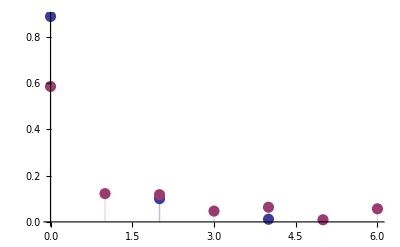

```mathematica
ListPlot[{ProbTeomAll[0.35],Table[{y-1,rho[[y,y]]},{y,1,n+1}]},PlotStyle-> {PointSize[0.02]},Filling->Axis, PlotRange->All]
```

```mathematica
(*reconstruct the Wigner function*)
```

```mathematica
Do[Rho[q,z]=rho[[q+1,z+1]],{q,0,n},{z,0,n}]
```

```mathematica
W[k_,l_,x_,y_]=(-1)^l/π*√((l!)/(k!))(√2*(x-ⅈ*y))^(k-l)*Exp[-(x^2+y^2)]*LaguerreL[l,k-l,2*(x^2+y^2)];
WMatrice[k_,l_,x_,y_]=If[k≥l,W[k,l,x,y],W[l,k,x,-y]]
Wigner[x_,y_]=∑_(k=0)^n ∑_(l=0)^n WMatrice[k,l,x,y]*Rho[k ,l];

Plot3D[Wigner[x,y],{x,-3,3},{y,-3,3},PlotRange->All]
```

If[k≥l,W[k,l,x,y],W[l,k,x,-y]]

-Graphics3D-

```mathematica
10^(-0.15/10)
```

0.966051